```mathematica
ClearAll["Global`*"]
```

## Todo: better sampling in order to have a nice uv map but a small obj file

#### The immersion has been computed elsewhere

```mathematica
(*y={u-2/3 Re[1/(Cos[v]-Cosh[u])] Sinh[u],+1/6 (7-8 Cos[v] Cosh[u]+Cos[2 v] Cosh[2 u]),1/6 ((5+Cos[2 v]) Cosh[2 u]-2 Cos[v] Cosh[u] (4+Cosh[2 u])) Re[1/(Cos[v]-Cosh[u])] Sin[v]}//FullSimplify[#,Element[{u,v},Reals]&&Cos[v]!=Cosh[u]]&//FullSimplify*)
f[{u_,v_}]={u-2/3 Re[1/(Cos[v]-Cosh[u])] Sinh[u],+1/6 (7-8 Cos[v] Cosh[u]+Cos[2 v] Cosh[2 u]),1/6 ((5+Cos[2 v]) Cosh[2 u]-2 Cos[v] Cosh[u] (4+Cosh[2 u])) Re[1/(Cos[v]-Cosh[u])] Sin[v]}//FullSimplify[#,Element[{u,v},Reals]&&Cos[v]!=Cosh[u]]&//FullSimplify
metric[{u_,v_}]=Norm[D[f[{u,v}],u]]^2 + Norm[D[f[{u,v}],v]]^2 //Simplify;
(*metric[{u_,v_}]:=1/147456 ⅇ^(-4 u) (4 ⅇ^(4 u) Abs[3 √((ⅇ^(-u-ⅈ v) (1+ⅇ^(u+ⅈ v))^2)/((-1+ⅇ^(u+ⅈ v))^2))+(√(ⅇ^(-u-ⅈ v)) (-9+7 ⅇ^(u+ⅈ v)))/(-1+ⅇ^(u+ⅈ v))]^2+Abs[6 √((ⅇ^(-u-ⅈ v) (1+ⅇ^(u+ⅈ v))^2)/((-1+ⅇ^(u+ⅈ v))^2))-(2 √(ⅇ^(-u-ⅈ v)) (-7+9 ⅇ^(u+ⅈ v)))/(-1+ⅇ^(u+ⅈ v))]^2)^2*)
gauss[{u_,v_}]:=(2 ⅇ^(2 u+2 ⅈ v) (3 √((ⅇ^(-u-ⅈ v) (1+ⅇ^(u+ⅈ v))^2)/((-1+ⅇ^(u+ⅈ v))^2))+(√(ⅇ^(-u-ⅈ v)) (-9+7 ⅇ^(u+ⅈ v)))/(-1+ⅇ^(u+ⅈ v))))/(6 √((ⅇ^(-u-ⅈ v) (1+ⅇ^(u+ⅈ v))^2)/((-1+ⅇ^(u+ⅈ v))^2))-(2 √(ⅇ^(-u-ⅈ v)) (-7+9 ⅇ^(u+ⅈ v)))/(-1+ⅇ^(u+ⅈ v)))
curvature[{u_,v_}]:=4/((1+Abs[gauss[{u,v}]]^2)^2)
```

{u-(2 Sinh[u])/(3 Cos[v]-3 Cosh[u]),1/6 (7-8 Cos[v] Cosh[u]+Cos[2 v] Cosh[2 u]),(((5+Cos[2 v]) Cosh[2 u]-2 Cos[v] Cosh[u] (4+Cosh[2 u])) Sin[v])/(6 (Cos[v]-Cosh[u]))}

```mathematica
plot = ParametricPlot3D[f[{u,v}],{u,0,Pi/2},{v,0,Pi},PlotPoints->{12,36},MaxRecursion->0,AxesLabel->{"x","y","z"},Mesh->All,RegionFunction->Function[{x,y,z,u,v},Norm[{x,y,z}]<20],PlotRange->All]
```

-Graphics3D-

#### a discrete domain with a pole at {0,0}

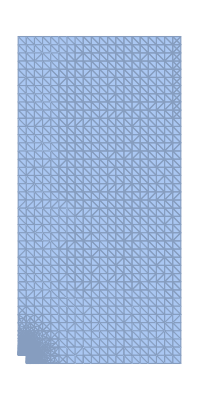

```mathematica
makeArray[j_,k_]:=Table[Table[1,k],j]
makeArrayWithPole[j_,k_]:=Join[makeArray[j-1,k],{Join[{0},Table[1,k-1]]}]
discreteRectangle = ArrayMesh[makeArrayWithPole[40,20],DataRange->{{0,Pi/2},{0,Pi}}];
curvatureRefinementFunction = Function[{vertices,area},area (curvature[{u,v}]/.{u->Mean[vertices][[1]],v->Mean[vertices][[2]]})>0.15];
metricRefinementFunction = Function[{vertices,area},area (metric[{u,v}]/.{u->Mean[vertices][[1]],v->Mean[vertices][[2]]})>0.25];
refinementFunction = Function[{vertices,area},metricRefinementFunction[vertices,area]||curvatureRefinementFunction[vertices,area]];
discreteDomain =TriangulateMesh[discreteRectangle,MeshRefinementFunction->refinementFunction]
```

#### Computing the surface data

```mathematica
points = MeshCoordinates[discreteDomain];
faces = MeshCells[discreteDomain,2];
pointsInSpace = f/@points;
surface=Graphics3D[{EdgeForm[],GraphicsComplex[pointsInSpace,faces]},Boxed->False,Axes->False]
```

-Graphics3D-

#### Exporting as JSONs

to make a uv map between 0 and 1:

```mathematica
max = Max[points];
min = Min[points];
lin[{u_,v_}]={(u-min)/(max-min), (v-min)/(max-min)};
```

```mathematica
facesList = faces[[All,1]];
data = {points, facesList, pointsInSpace};
Export["/home/thomas/python/objParser/input/faces.json",facesList]
Export["/home/thomas/python/objParser/input/points.json",pointsInSpace]
Export["/home/thomas/python/objParser/input/uv.json",lin/@points]
```

/home/thomas/python/objParser/input/faces.json

/home/thomas/python/objParser/input/points.json

/home/thomas/python/objParser/input/uv.json

#### Run obj-helper.py to get the obj.